```mathematica
Needs["PlotLegends`"]
```

### Equation

a(x,y) u_x+b(x,y)u_y=c(x,y,u(x,y))

```mathematica
a[x_,y_]:=10 y^2-12x+1
b[x_,y_]:=1+y
c[x_,y_,z_]:=μ z
```

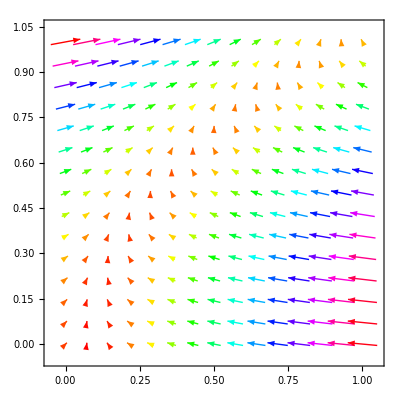

```mathematica
VectorPlot[{a[x,y],b[x,y]},{x,0,1},{y,0,1},VectorColorFunction->Hue]
```

### System describing the evolution of characteristics

Incoming boundary: 	left, bottom and right side of rectangle (0,1)×(0,1); parametrized by a curve  {γ_1(r), γ_2(r), 0≤ r≤1}
Boundary condition:	z(r,0), 0≤r≤1

```mathematica
Subscript[γ, 1][r_]:=Piecewise[{{0, 0≤r<1}, {r-1, 1≤r<2}, {1, 2≤r≤3}}];
Subscript[γ, 2][r_]:=Piecewise[{{1-r, 0≤r<1}, {0, 1≤r<2}, {r-2, 2≤r≤3}}];
```

```mathematica
ϕ[r_]:=Piecewise[{{UnitStep[r-1/2], 0≤r<1}, {1-UnitStep[r-3/2], 1≤r<2}, {Sin[π(r-2)]^2, 2≤r≤3}}];
```

```mathematica
system={
D[x[r,s],s]==a[x[r,s],y[r,s]],x[r,0]==Subscript[γ, 1][r],
D[y[r,s],s]==b[x[r,s],y[r,s]],y[r,0]==Subscript[γ, 2][r],
D[z[r,s],s]==c[x[r,s],y[r,s],z[r,s]],z[r,0]==ϕ[r]
};
```

The boundary curve is non-characteristic, i.e. it is nowhere tangent to the projection of  a characteristic into the xy plane

```mathematica
Resolve[Exists[r,0≤r≤3&&{a[Subscript[γ, 1][r],Subscript[γ, 2][r]],b[Subscript[γ, 1][r],Subscript[γ, 2][r]]}.{-Subscript[γ, 2]'[r],Subscript[γ, 1]'[r]}==0]]
```

False

### Parametrization of the integral surface

- union of all characteristics emanating from the boundary curve

```mathematica
charsol=Flatten[DSolve[system,{x,y,z},{r,s}]]
```

{y→Function[{r,s},-1+ⅇ^s+ⅇ^s (Piecewise[{{1-r, 0≤r<1}, {0, 1≤r<2}, {-2+r, 2≤r≤3}, {0, True}}])],x→Function[{r,s},1/1092 ⅇ^(-12 s) (-101+1001 ⅇ^(12 s)-1680 ⅇ^(13 s)+780 ⅇ^(14 s)+1092 (Piecewise[{{0, 0≤r<1}, {-1+r, 1≤r<2}, {1, 2≤r≤3}, {0, True}}])+120 (Piecewise[{{1-r, 0≤r<1}, {0, 1≤r<2}, {-2+r, 2≤r≤3}, {0, True}}])-1680 ⅇ^(13 s) (Piecewise[{{1-r, 0≤r<1}, {0, 1≤r<2}, {-2+r, 2≤r≤3}, {0, True}}])+1560 ⅇ^(14 s) (Piecewise[{{1-r, 0≤r<1}, {0, 1≤r<2}, {-2+r, 2≤r≤3}, {0, True}}])-780 (Piecewise[{{1-r, 0≤r<1}, {0, 1≤r<2}, {-2+r, 2≤r≤3}, {0, True}}])^2+780 ⅇ^(14 s) (Piecewise[{{1-r, 0≤r<1}, {0, 1≤r<2}, {-2+r, 2≤r≤3}, {0, True}}])^2)],z→Function[{r,s},ⅇ^(s μ) (Piecewise[{{UnitStep[-1/2+r], 0≤r<1}, {1-UnitStep[-3/2+r], 1≤r<2}, {Sin[π (-2+r)]^2, 2≤r≤3}, {0, True}}])]}

## Construction of mapping [x(r,s),y(r,s)]↦[r(x,y),s(x,y)]

Let p=ⅇ^s. We will rewrite the equations for x,y for each part of the interval for r separately. Following is the definition of z=z(r,p):

```mathematica
zrp:=z/.charsol[[3]]/.{ⅇ^(s m_)->p^m,s->p}
```

### 0≤r<1

```mathematica
eqn1={
1092x==p^-12(-101+1001 p^12-1680 p^13+780 p^14+120 q-1680 p^13 q+1560 p^14 q-780 q^2+780 p^14 q^2),
y==p+p q-1
}/.q->(1-r)
```

{1092 x==(-101+1001 p^12-1680 p^13+780 p^14+120 (1-r)-1680 p^13 (1-r)+1560 p^14 (1-r)-780 (1-r)^2+780 p^14 (1-r)^2)/p^12,y==-1+p+p (1-r)}

#### Check local invertibility around every point of the current rpdomain

We have bounds on r,y (but not apriori on p). However, from the second eqn. in eqn1, we may easily determine p=p(r,y) and check local invertibility of the mapping [r,p]↦[x,y] for any admissible r,y. Although we could then use p(r,y) in the first eqn. in system eqn1 to obtain r=r(x,y), we will rather later let Mathematica solve the system automatically (a more efficiently computable expression will be obtained this way).  Note that since p=ⅇ^s, ln(p(r,y)) gives the value of parameter s for which the characteristic starting at [x(r,0),y(r,0)] reaches point [x(r,s),y]. We thus allow p ∈[1,∞), i.e. we start following the characteristic from the point where it enters the domain.

```mathematica
pry1[r_, y_] := Evaluate[If[#<1,None,#]&[p /. First[Assuming[0≤ y≤1 && 0≤r< 1, Refine[Solve[eqn1[[2]], p]]]]]]
xrp1[r_,p_]:=Evaluate[x/.First[Solve[eqn1,x]]]
yrp1[r_,p_]:=Evaluate[y/.First[Solve[eqn1,y]]]
```

The first of the following graphs shows the value of s for which we get to y along the characteristic starting at [x(r, 0), y(r, 0)]. The second and third shows the corresponding x and z coordinates (the latter is the solution of our equation).

```mathematica
GraphicsRow[{
Plot3D[Log[pry1[r,y]],{r,0,1},{y,0,1},AxesLabel->{r,y,Log[p]},PlotLabel->Log[p[r,y]]],
Plot3D[xrp1[r,pry1[r,y]],{r,0,1},{y,0,1},AxesLabel->{r,y,x},PlotLabel->x[r,p[r,y]]],
Block[{μ=0},Plot3D[If[#<1,None,zrp[r,#]]&[pry1[r,y]],{r,0,1},{y,0,1},AxesLabel->{r,y,z},PlotLabel->z[r,p[r,y]]]]
}]
```

-Graphics-

##### The local inverse mapping around [r,p] will exist whenever the following Jacobian is nonzero

Note that x_p(r,p)=a(x(r,p),y(r,p)) and y_p(r,p)=b(x(r,p),y(r,p)) since x,y satisfy the characteristic ODE's.

```mathematica
Jac[r_,y_]:=Det[({{D[xrp1[t,pry1[r,y]],t]/.t->r, a[xrp1[r,pry1[r,y]],yrp1[r,pry1[r,y]]]}, {D[yrp1[t,pry1[r,y]],t]/.t->r, b[xrp1[r,pry1[r,y]],yrp1[r,pry1[r,y]]]}})]
```

```mathematica
Resolve[Exists[{r,y},0≤r<1&&0≤y≤1&&Jac[r,y]==0]]
```

False

```mathematica
Plot3D[Jac[r,y],{r,0,1},{y,0,1}]
```

-Graphics3D-

#### Invert the characteristics, i.e. compute the mapping [x(r, p), y(r, p)] ↦ [r(x, y), p(x, y)]

```mathematica
sln1=Assuming[0≤r<1&&p>1&&0≤x≤1&&0≤y≤1,Refine[Solve[eqn1,{p,r}]]]
```

{{r→(-1-y+2 Root[-780-1560 y-780 y^2+(1680+1680 y) #1-1001 #1^2+(101-1092 x-120 y+780 y^2) #1^14&,1])/Root[-780-1560 y-780 y^2+(1680+1680 y) #1-1001 #1^2+(101-1092 x-120 y+780 y^2) #1^14&,1],p→Root[-780-1560 y-780 y^2+(1680+1680 y) #1-1001 #1^2+(101-1092 x-120 y+780 y^2) #1^14&,1]},{r→(-1-y+2 Root[-780-1560 y-780 y^2+(1680+1680 y) #1-1001 #1^2+(101-1092 x-120 y+780 y^2) #1^14&,2])/Root[-780-1560 y-780 y^2+(1680+1680 y) #1-1001 #1^2+(101-1092 x-120 y+780 y^2) #1^14&,2],p→Root[-780-1560 y-780 y^2+(1680+1680 y) #1-1001 #1^2+(101-1092 x-120 y+780 y^2) #1^14&,2]},{r→(-1-y+2 Root[-780-1560 y-780 y^2+(1680+1680 y) #1-1001 #1^2+(101-1092 x-120 y+780 y^2) #1^14&,3])/Root[-780-1560 y-780 y^2+(1680+1680 y) #1-1001 #1^2+(101-1092 x-120 y+780 y^2) #1^14&,3],p→Root[-780-1560 y-780 y^2+(1680+1680 y) #1-1001 #1^2+(101-1092 x-120 y+780 y^2) #1^14&,3]},{r→(-1-y+2 Root[-780-1560 y-780 y^2+(1680+1680 y) #1-1001 #1^2+(101-1092 x-120 y+780 y^2) #1^14&,4])/Root[-780-1560 y-780 y^2+(1680+1680 y) #1-1001 #1^2+(101-1092 x-120 y+780 y^2) #1^14&,4],p→Root[-780-1560 y-780 y^2+(1680+1680 y) #1-1001 #1^2+(101-1092 x-120 y+780 y^2) #1^14&,4]},{r→(-1-y+2 Root[-780-1560 y-780 y^2+(1680+1680 y) #1-1001 #1^2+(101-1092 x-120 y+780 y^2) #1^14&,5])/Root[-780-1560 y-780 y^2+(1680+1680 y) #1-1001 #1^2+(101-1092 x-120 y+780 y^2) #1^14&,5],p→Root[-780-1560 y-780 y^2+(1680+1680 y) #1-1001 #1^2+(101-1092 x-120 y+780 y^2) #1^14&,5]},{r→(-1-y+2 Root[-780-1560 y-780 y^2+(1680+1680 y) #1-1001 #1^2+(101-1092 x-120 y+780 y^2) #1^14&,6])/Root[-780-1560 y-780 y^2+(1680+1680 y) #1-1001 #1^2+(101-1092 x-120 y+780 y^2) #1^14&,6],p→Root[-780-1560 y-780 y^2+(1680+1680 y) #1-1001 #1^2+(101-1092 x-120 y+780 y^2) #1^14&,6]},{r→(-1-y+2 Root[-780-1560 y-780 y^2+(1680+1680 y) #1-1001 #1^2+(101-1092 x-120 y+780 y^2) #1^14&,7])/Root[-780-1560 y-780 y^2+(1680+1680 y) #1-1001 #1^2+(101-1092 x-120 y+780 y^2) #1^14&,7],p→Root[-780-1560 y-780 y^2+(1680+1680 y) #1-1001 #1^2+(101-1092 x-120 y+780 y^2) #1^14&,7]},{r→(-1-y+2 Root[-780-1560 y-780 y^2+(1680+1680 y) #1-1001 #1^2+(101-1092 x-120 y+780 y^2) #1^14&,8])/Root[-780-1560 y-780 y^2+(1680+1680 y) #1-1001 #1^2+(101-1092 x-120 y+780 y^2) #1^14&,8],p→Root[-780-1560 y-780 y^2+(1680+1680 y) #1-1001 #1^2+(101-1092 x-120 y+780 y^2) #1^14&,8]},{r→(-1-y+2 Root[-780-1560 y-780 y^2+(1680+1680 y) #1-1001 #1^2+(101-1092 x-120 y+780 y^2) #1^14&,9])/Root[-780-1560 y-780 y^2+(1680+1680 y) #1-1001 #1^2+(101-1092 x-120 y+780 y^2) #1^14&,9],p→Root[-780-1560 y-780 y^2+(1680+1680 y) #1-1001 #1^2+(101-1092 x-120 y+780 y^2) #1^14&,9]},{r→(-1-y+2 Root[-780-1560 y-780 y^2+(1680+1680 y) #1-1001 #1^2+(101-1092 x-120 y+780 y^2) #1^14&,10])/Root[-780-1560 y-780 y^2+(1680+1680 y) #1-1001 #1^2+(101-1092 x-120 y+780 y^2) #1^14&,10],p→Root[-780-1560 y-780 y^2+(1680+1680 y) #1-1001 #1^2+(101-1092 x-120 y+780 y^2) #1^14&,10]},{r→(-1-y+2 Root[-780-1560 y-780 y^2+(1680+1680 y) #1-1001 #1^2+(101-1092 x-120 y+780 y^2) #1^14&,11])/Root[-780-1560 y-780 y^2+(1680+1680 y) #1-1001 #1^2+(101-1092 x-120 y+780 y^2) #1^14&,11],p→Root[-780-1560 y-780 y^2+(1680+1680 y) #1-1001 #1^2+(101-1092 x-120 y+780 y^2) #1^14&,11]},{r→(-1-y+2 Root[-780-1560 y-780 y^2+(1680+1680 y) #1-1001 #1^2+(101-1092 x-120 y+780 y^2) #1^14&,12])/Root[-780-1560 y-780 y^2+(1680+1680 y) #1-1001 #1^2+(101-1092 x-120 y+780 y^2) #1^14&,12],p→Root[-780-1560 y-780 y^2+(1680+1680 y) #1-1001 #1^2+(101-1092 x-120 y+780 y^2) #1^14&,12]},{r→(-1-y+2 Root[-780-1560 y-780 y^2+(1680+1680 y) #1-1001 #1^2+(101-1092 x-120 y+780 y^2) #1^14&,13])/Root[-780-1560 y-780 y^2+(1680+1680 y) #1-1001 #1^2+(101-1092 x-120 y+780 y^2) #1^14&,13],p→Root[-780-1560 y-780 y^2+(1680+1680 y) #1-1001 #1^2+(101-1092 x-120 y+780 y^2) #1^14&,13]},{r→(-1-y+2 Root[-780-1560 y-780 y^2+(1680+1680 y) #1-1001 #1^2+(101-1092 x-120 y+780 y^2) #1^14&,14])/Root[-780-1560 y-780 y^2+(1680+1680 y) #1-1001 #1^2+(101-1092 x-120 y+780 y^2) #1^14&,14],p→Root[-780-1560 y-780 y^2+(1680+1680 y) #1-1001 #1^2+(101-1092 x-120 y+780 y^2) #1^14&,14]}}

```mathematica
rs1:=Table[r/.sln1[[n,1]],{n,1,Length[sln1]}]
ps1:=Table[p/.sln1[[n,2]],{n,1,Length[sln1]}]
```

```mathematica
rvals1[x_,y_]:=Evaluate[rs1]
pvals1[x_,y_]:=Evaluate[ps1]
```

#### Pick only real r's lying in the currently investigated interval

We also pick the corresponding p.

```mathematica
admis1=Function[MatchQ[#,_Real]&&0≤#<1];
```

```mathematica
radmislist1[x_,y_]:=Select[rvals1[x,y],admis1]
padmislist1[x_,y_]:=Pick[pvals1[x,y],Map[admis1,rvals1[x,y]]]
```

```mathematica
(*ShowLegend[ContourPlot[Length[radmislist1[x,y]],{x,0,1},{y,0,1},FrameLabel->{x,y},PlotLabel->"number of valid r's"],{ColorData["LakeColors"][#1]&,2,"0","1",LegendPosition->{1.1,-0.4}}]*)
```

#### Define r(x,y), p(x,y)

```mathematica
radmis1:=Function[{x,y},If[Length[#]==0,0,#[[1]]]&[radmislist1[x,y]]]
(*padmis1:=Function[{x,y},pry1[radmis1[x,y],y]]*)
padmis1:=Function[{x,y},If[Length[#]==0||#[[1]]<1,0,#[[1]]]&[padmislist1[x,y]]]
```

### 1≤r<2

```mathematica
eqn2={
1092x == p^-12(-101+1001 p^12-1680 p^13+780 p^14-1092(1-r)),
y==p-1
}
```

{1092 x==(-101+1001 p^12-1680 p^13+780 p^14-1092 (1-r))/p^12,y==-1+p}

#### Check local invertibility around every point of the current rpdomain

```mathematica
pry2[r_, y_] := Evaluate[If[#<1,None,#]&[p /. First[Assuming[0≤ y≤1 && 1≤r≤2, Refine[Solve[eqn2[[2]], p]]]]]]
```

```mathematica
xrp2[r_,p_]:=Evaluate[x/.First[Solve[eqn2,x]]]
yrp2[r_,p_]:=Evaluate[y/.First[Solve[eqn2,y]]]
```

```mathematica
GraphicsRow[{
Plot3D[Log[pry2[r,y]],{r,1,2},{y,0,1},AxesLabel->{r,y,Log[p]},PlotLabel->Log[p[r,y]]],
Plot3D[xrp2[r,pry2[r,y]],{r,1,2},{y,0,1},AxesLabel->{r,y,x},PlotLabel->x[r,p[r,y]]],
Block[{μ=0},Plot3D[If[#<1,None,zrp[r,#]]&[pry2[r,y]],{r,1,2},{y,0,1},AxesLabel->{r,y,z},PlotLabel->z[r,p[r,y]]]]
}]
```

-Graphics-

##### The local inverse mapping around [r,p] will exist whenever the following Jacobian is nonzero

```mathematica
Jac[r_,y_]:=Det[({{D[xrp2[t,pry2[r,y]],t]/.t->r, a[xrp2[r,pry2[r,y]],yrp2[r,pry2[r,y]]]}, {D[yrp2[t,pry2[r,y]],t]/.t->r, b[xrp2[r,pry2[r,y]],yrp2[r,pry2[r,y]]]}})]
```

```mathematica
Resolve[Exists[{r,y},1≤r<2&&0≤y≤1&&Jac[r,y]==0]]
```

False

```mathematica
Plot3D[Jac[r,y],{r,1,2},{y,0,1}]
```

-Graphics3D-

#### Compute the inverse mapping

```mathematica
sln2=Assuming[1≤r<2&&p>1&&0≤x≤1&&0≤y≤1,Refine[Solve[eqn2,{p,r}]]]//Expand//First
```

{r→1+x-y+12 x y-(11 y^2)/2+66 x y^2-(65 y^3)/3+220 x y^3-(275 y^4)/4+495 x y^4-176 y^5+792 x y^5-352 y^6+924 x y^6-(3762 y^7)/7+792 x y^7-(2475 y^8)/4+495 x y^8-(1595 y^9)/3+220 x y^9-(671 y^10)/2+66 x y^10-151 y^11+12 x y^11-(551 y^12)/12+x y^12-(110 y^13)/13-(5 y^14)/7,p→1+y}

```mathematica
radmisfn2[x_,y_]:=Evaluate[r/.sln2[[1]]]
padmisfn2[x_,y_]:=Evaluate[p/.sln2[[2]]]
```

```mathematica
radmis2:=Function[{x,y},If[1≤#<2,#,0]&[radmisfn2[x,y]]]
padmis2:=Function[{x,y},If[radmis2[x,y]==0||#<1,0,#]&[padmisfn2[x,y]]]
```

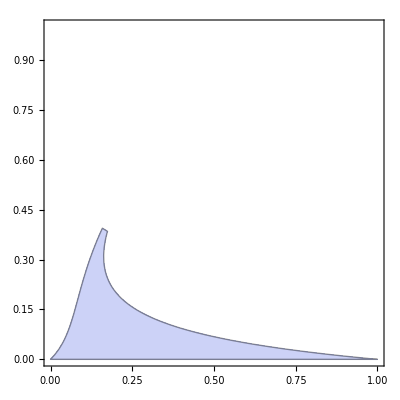

```mathematica
RegionPlot[1≤r<2/.sln2,{x,0,1},{y,0,1}]
```

### 2≤r≤3

```mathematica
eqn3={
1092x==p^-12(-101+1001 p^12-1680 p^13+780 p^14+1092+120(r-2)-1680(r-2) p^13+1560(r-2) p^14-780(r-2)^2+780(r-2)^2 p^14),
y==p+(r-2) p-1
}
```

{1092 x==(991+1001 p^12-1680 p^13+780 p^14+120 (-2+r)-1680 p^13 (-2+r)+1560 p^14 (-2+r)-780 (-2+r)^2+780 p^14 (-2+r)^2)/p^12,y==-1+p+p (-2+r)}

#### Check local invertibility around every point of the current rpdomain

```mathematica
pry3[r_, y_] := Evaluate[If[#<1,None,#]&[p /. First[Assuming[0≤ y≤1 && 2≤r≤3, Refine[Solve[eqn3[[2]], p]]]]]]
```

```mathematica
xrp3[r_,p_]:=Evaluate[x/.First[Solve[eqn3,x]]]
yrp3[r_,p_]:=Evaluate[y/.First[Solve[eqn3,y]]]
```

```mathematica
GraphicsRow[{
Plot3D[Log[pry3[r,y]],{r,2,3},{y,0,1},AxesLabel->{r,y,Log[p]},PlotLabel->Log[p[r,y]]],
Plot3D[xrp3[r,pry3[r,y]],{r,2,3},{y,0,1},AxesLabel->{r,y,x},PlotLabel->x[r,p[r,y]]],
Block[{μ=0},Plot3D[If[#<1,None,zrp[r,#]]&[pry3[r,y]],{r,2,3},{y,0,1},AxesLabel->{r,y,z},PlotLabel->z[r,p[r,y]]]]
}]
```

-Graphics-

##### The local inverse mapping around [r,p] will exist whenever the following Jacobian is nonzero

```mathematica
Jac[r_,y_]:=Det[({{D[xrp3[t,pry3[r,y]],t]/.t->r, a[xrp3[r,pry3[r,y]],yrp3[r,pry3[r,y]]]}, {D[yrp3[t,pry3[r,y]],t]/.t->r, b[xrp3[r,pry3[r,y]],yrp3[r,pry3[r,y]]]}})]
```

```mathematica
Resolve[Exists[{r,y},2≤r<3&&0≤y≤1&&Jac[r,y]==0]]
```

False

```mathematica
Plot3D[Jac[r,y],{r,2,3},{y,0,1}]
```

-Graphics3D-

#### Compute the inverse mapping

```mathematica
sln3=Assuming[2≤r≤3&&p>1&&0≤x≤1&&0≤y≤1,Refine[Solve[eqn3,{p,r}]]]
```

{{r→(1+y+Root[-780-1560 y-780 y^2+(1680+1680 y) #1+91 #1^2+(101-1092 x-120 y+780 y^2) #1^14&,1])/Root[-780-1560 y-780 y^2+(1680+1680 y) #1+91 #1^2+(101-1092 x-120 y+780 y^2) #1^14&,1],p→Root[-780-1560 y-780 y^2+(1680+1680 y) #1+91 #1^2+(101-1092 x-120 y+780 y^2) #1^14&,1]},{r→(1+y+Root[-780-1560 y-780 y^2+(1680+1680 y) #1+91 #1^2+(101-1092 x-120 y+780 y^2) #1^14&,2])/Root[-780-1560 y-780 y^2+(1680+1680 y) #1+91 #1^2+(101-1092 x-120 y+780 y^2) #1^14&,2],p→Root[-780-1560 y-780 y^2+(1680+1680 y) #1+91 #1^2+(101-1092 x-120 y+780 y^2) #1^14&,2]},{r→(1+y+Root[-780-1560 y-780 y^2+(1680+1680 y) #1+91 #1^2+(101-1092 x-120 y+780 y^2) #1^14&,3])/Root[-780-1560 y-780 y^2+(1680+1680 y) #1+91 #1^2+(101-1092 x-120 y+780 y^2) #1^14&,3],p→Root[-780-1560 y-780 y^2+(1680+1680 y) #1+91 #1^2+(101-1092 x-120 y+780 y^2) #1^14&,3]},{r→(1+y+Root[-780-1560 y-780 y^2+(1680+1680 y) #1+91 #1^2+(101-1092 x-120 y+780 y^2) #1^14&,4])/Root[-780-1560 y-780 y^2+(1680+1680 y) #1+91 #1^2+(101-1092 x-120 y+780 y^2) #1^14&,4],p→Root[-780-1560 y-780 y^2+(1680+1680 y) #1+91 #1^2+(101-1092 x-120 y+780 y^2) #1^14&,4]},{r→(1+y+Root[-780-1560 y-780 y^2+(1680+1680 y) #1+91 #1^2+(101-1092 x-120 y+780 y^2) #1^14&,5])/Root[-780-1560 y-780 y^2+(1680+1680 y) #1+91 #1^2+(101-1092 x-120 y+780 y^2) #1^14&,5],p→Root[-780-1560 y-780 y^2+(1680+1680 y) #1+91 #1^2+(101-1092 x-120 y+780 y^2) #1^14&,5]},{r→(1+y+Root[-780-1560 y-780 y^2+(1680+1680 y) #1+91 #1^2+(101-1092 x-120 y+780 y^2) #1^14&,6])/Root[-780-1560 y-780 y^2+(1680+1680 y) #1+91 #1^2+(101-1092 x-120 y+780 y^2) #1^14&,6],p→Root[-780-1560 y-780 y^2+(1680+1680 y) #1+91 #1^2+(101-1092 x-120 y+780 y^2) #1^14&,6]},{r→(1+y+Root[-780-1560 y-780 y^2+(1680+1680 y) #1+91 #1^2+(101-1092 x-120 y+780 y^2) #1^14&,7])/Root[-780-1560 y-780 y^2+(1680+1680 y) #1+91 #1^2+(101-1092 x-120 y+780 y^2) #1^14&,7],p→Root[-780-1560 y-780 y^2+(1680+1680 y) #1+91 #1^2+(101-1092 x-120 y+780 y^2) #1^14&,7]},{r→(1+y+Root[-780-1560 y-780 y^2+(1680+1680 y) #1+91 #1^2+(101-1092 x-120 y+780 y^2) #1^14&,8])/Root[-780-1560 y-780 y^2+(1680+1680 y) #1+91 #1^2+(101-1092 x-120 y+780 y^2) #1^14&,8],p→Root[-780-1560 y-780 y^2+(1680+1680 y) #1+91 #1^2+(101-1092 x-120 y+780 y^2) #1^14&,8]},{r→(1+y+Root[-780-1560 y-780 y^2+(1680+1680 y) #1+91 #1^2+(101-1092 x-120 y+780 y^2) #1^14&,9])/Root[-780-1560 y-780 y^2+(1680+1680 y) #1+91 #1^2+(101-1092 x-120 y+780 y^2) #1^14&,9],p→Root[-780-1560 y-780 y^2+(1680+1680 y) #1+91 #1^2+(101-1092 x-120 y+780 y^2) #1^14&,9]},{r→(1+y+Root[-780-1560 y-780 y^2+(1680+1680 y) #1+91 #1^2+(101-1092 x-120 y+780 y^2) #1^14&,10])/Root[-780-1560 y-780 y^2+(1680+1680 y) #1+91 #1^2+(101-1092 x-120 y+780 y^2) #1^14&,10],p→Root[-780-1560 y-780 y^2+(1680+1680 y) #1+91 #1^2+(101-1092 x-120 y+780 y^2) #1^14&,10]},{r→(1+y+Root[-780-1560 y-780 y^2+(1680+1680 y) #1+91 #1^2+(101-1092 x-120 y+780 y^2) #1^14&,11])/Root[-780-1560 y-780 y^2+(1680+1680 y) #1+91 #1^2+(101-1092 x-120 y+780 y^2) #1^14&,11],p→Root[-780-1560 y-780 y^2+(1680+1680 y) #1+91 #1^2+(101-1092 x-120 y+780 y^2) #1^14&,11]},{r→(1+y+Root[-780-1560 y-780 y^2+(1680+1680 y) #1+91 #1^2+(101-1092 x-120 y+780 y^2) #1^14&,12])/Root[-780-1560 y-780 y^2+(1680+1680 y) #1+91 #1^2+(101-1092 x-120 y+780 y^2) #1^14&,12],p→Root[-780-1560 y-780 y^2+(1680+1680 y) #1+91 #1^2+(101-1092 x-120 y+780 y^2) #1^14&,12]},{r→(1+y+Root[-780-1560 y-780 y^2+(1680+1680 y) #1+91 #1^2+(101-1092 x-120 y+780 y^2) #1^14&,13])/Root[-780-1560 y-780 y^2+(1680+1680 y) #1+91 #1^2+(101-1092 x-120 y+780 y^2) #1^14&,13],p→Root[-780-1560 y-780 y^2+(1680+1680 y) #1+91 #1^2+(101-1092 x-120 y+780 y^2) #1^14&,13]},{r→(1+y+Root[-780-1560 y-780 y^2+(1680+1680 y) #1+91 #1^2+(101-1092 x-120 y+780 y^2) #1^14&,14])/Root[-780-1560 y-780 y^2+(1680+1680 y) #1+91 #1^2+(101-1092 x-120 y+780 y^2) #1^14&,14],p→Root[-780-1560 y-780 y^2+(1680+1680 y) #1+91 #1^2+(101-1092 x-120 y+780 y^2) #1^14&,14]}}

```mathematica
rs3:=Table[r/.sln3[[n,1]],{n,1,Length[sln3]}]
ps3:=Table[p/.sln3[[n,2]],{n,1,Length[sln3]}]
```

```mathematica
rvals3[x_,y_]:=Evaluate[rs3]
pvals3[x_,y_]:=Evaluate[ps3]
```

```mathematica
admis3=Function[MatchQ[#,_Real]&&2≤#≤3];
```

```mathematica
radmislist3[x_,y_]:=Select[rvals3[x,y],admis3]
padmislist3[x_,y_]:=Pick[pvals3[x,y],Map[admis3,rvals3[x,y]]]
```

```mathematica
(*ShowLegend[ContourPlot[Length[radmislist3[x,y]],{x,0,1},{y,0,1},FrameLabel->{x,y},PlotLabel->"number of valid r's"],{ColorData["LakeColors"][#1]&,2,"0","1",LegendPosition->{1.1,-0.4}}]*)
```

```mathematica
radmis3:=Function[{x,y},If[Length[#]==0,0,#[[1]]]&[radmislist3[x,y]]]
(*padmis3:=Function[{x,y},pry3[radmis3[x,y],y]]*)
padmis3:=Function[{x,y},If[Length[#]==0||#[[1]]<1,0,#[[1]]]&[padmislist3[x,y]]]
```

```mathematica
rfinal[x_,y_]:=Evaluate[radmis1[x,y]]+radmis2[x,y]+Evaluate[radmis3[x,y]]
pfinal[x_,y_]:=padmis1[x,y]+padmis2[x,y]+padmis3[x,y]
```

```mathematica
(*Monitor[
GraphicsRow[{
ShowLegend[
ContourPlot[rfinal[x,y],{x,0,1},{y,0,1},ColorFunction->"Rainbow",FrameLabel->{x,y},PlotLabel->r],{ColorData["Rainbow"][#1]&,15,"0","3",LegendPosition->{1.1,-0.4}}
],
Plot3D[pfinal[x,y],{x,0,1},{y,0,1},ColorFunction->"Rainbow",AxesLabel->{x,y,p},PlotLabel->p,PlotRange->All]
}],
TableForm[{x,y},TableHeadings->{{"x","y"},None}]
]*)
```

## Final solution

```mathematica
u[x_?NumericQ,y_?NumericQ]:=zrp[rfinal[x,y],pfinal[x,y]]
```

```mathematica
μ=0
```

0

```mathematica
uc=Compile[{{x,_Real},{y,_Real}},u[x,y]]
```

CompiledFunction[{x,y},u[x,y],-CompiledCode-]

```mathematica
(*Block[
{evals = 0},
Monitor[
Timing[
Plot3D[uc[x,y],{x,0,1},{y,0,1},MaxRecursion->4,EvaluationMonitor:>evals++, PlotLabel:>ToString[evals]<>" evaluations",AxesLabel->{"x","y"}]
],
TableForm[{x,y,evals},TableHeadings->{{"x","y","evals"},None}]
]
]*)
```

```mathematica
(*Timing[Export["sol_100x100.map", 
Monitor[
Flatten[
Table[
Table[
{x,y,Chop[u[x,y]]},{x,0,1,0.01}
],{y,0,1,0.01}
],
1],{x,y}
],"Table"
]]*)
```

```mathematica
(*Export["outflow_profile_100.map", Table[{x,Chop[u[x,1]]},{x,0,1,0.01}],"Table"]*)
```

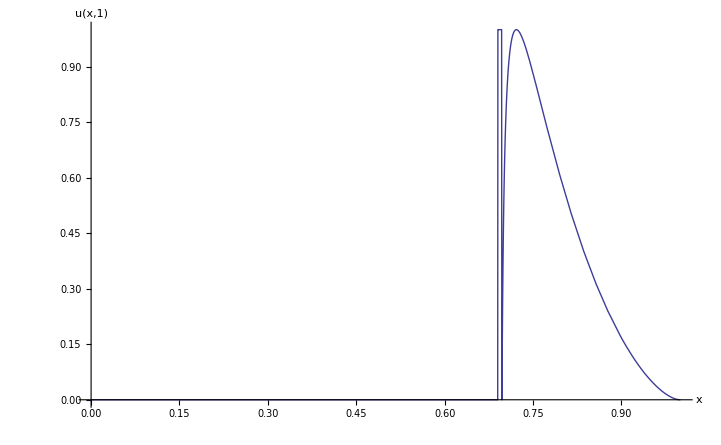

```mathematica
Plot[uc[x,1],{x,0,1},AxesLabel->{"x","u(x,1)"},PlotRange->All]
```

```mathematica
Monitor[NIntegrate[b[x,1]uc[x,1] Sin[(π x)/2],{x,0,0.69,0.7,1},MaxRecursion->20],x]
```

CompiledFunction::cfsa: Argument x at position 1 should be a machine-size real number.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

0.2465